```mathematica
deps1=ReadList["D:\\Grofs\\dependencies1.txt",Expression];Length[deps1]
"OK"
```

1177251

OK

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression];Length[deps2]
```

1365053

```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression];Length[deps3]
```

2436995

```mathematica
rule1=DeleteDuplicates[Map[#[[2]]&,deps1]]
```

{1,2,3,5,8,9,6,13,16,12,17,10,20,14,19,15,11,22,23,32,29,27,33,28,34,42,43,44,31,26,45,39,51,50,52,48,53,54,47,24,58,59,60,61,57,25,30,63,64,49,35,65,66,67,69,70,71,68,38,36,37,73,77,74,83,392678,390827,398388,320022,398386,398389,320023,369799,390029,370169,398392,398391,398390,398393,398068,390862,398394,398395,398396,390021,398398,398397,398399,398401,398400,398403,398402,398404,398405,398406,390820,398407,398050,398408,398409,398410,397439,336881,398411,398412,398414,398415,398413,398416,398418,398417,398419,398421,398422,398420,398423,398425,398424,398426,398428,398429,398427,398430,398431,398432,398433,398434,398435,398436,394827,398438}
 |  |  |  |

```mathematica
rule2=DeleteDuplicates[Map[#[[2]]&,deps2]]
```

{2,3,4,5,6,7,8,10,11,12,13,14,15,18,21,22,20,16,17,24,25,26,27,28,29,30,31,37,38,36,39,40,41,47,48,49,50,43,54,55,56,57,62,44,32,42,51,60,65,64,59,63,61,68,52,58,46,35,45,72,73,69,74,75,76,383366,398386,398387,398389,398390,398391,398388,398394,398397,398392,398398,398393,398395,398400,398396,398402,398403,398399,398404,398406,398407,398408,398410,398409,398413,398411,398401,398416,398417,398412,398420,398414,398421,398415,398422,398405,398424,398418,398425,398419,398427,398428,398429,398423,398431,398430,398432,398383,398426,398433,298130,298146,398338,398434,398285,341728,397976,398435,390258,373206,373252,373205,373214,373244,398437,398438}
 |  |  |  |

```mathematica
Max[rule1]
```

398438

```mathematica
Max[rule2]
```

398438

```mathematica
onlyRule5=Complement[Range[398438],rule1,rule2]
```

{6985,279676}

```mathematica
FindGraph[GraphData["IcosahedralGraph"],1,10000]
```

6985

```mathematica
deps3Bis=ReadList["D:\\Grofs\\dependencies-more3.txt",Expression];Length[deps3Bis]
```

3376051

```mathematica
pentagonRuleTransitions=Sort[Join[Select[deps3,MemberQ[{6985,279676}, #[[2]]]&],Select[deps3Bis,MemberQ[{6985,279676}, #[[2]]]&]]]
```

{{897,6985,{3,{4,5,7,10,9},{5<->9,5<->10},{{4,5,9},{5,9,10},{5,7,10}}}},{897,6985,{3,{4,5,7,11,8},{5<->8,5<->11},{{4,5,8},{5,8,11},{5,7,11}}}},{897,6985,{3,{7,5,4,8,11},{5<->11,5<->8},{{5,7,11},{5,8,11},{4,5,8}}}},{897,6985,{3,{7,5,4,9,10},{5<->10,5<->9},{{5,7,10},{5,9,10},{4,5,9}}}},{29870,279676,{3,{10,5,11,2,9},{5<->9,2<->5},{{5,9,10},{2,5,9},{2,5,11}}}},{29870,279676,{3,{11,5,10,9,2},{2<->5,5<->9},{{2,5,11},{2,5,9},{5,9,10}}}},{31317,279676,{3,{1,2,11,5,7},{2<->7,2<->5},{{1,2,7},{2,5,7},{2,5,11}}}},{31317,279676,{3,{11,2,1,7,5},{2<->5,2<->7},{{2,5,11},{2,5,7},{1,2,7}}}},{32637,279676,{3,{1,3,6,8,12},{3<->12,3<->8},{{1,3,12},{3,8,12},{3,6,8}}}},{32637,279676,{3,{1,7,5,11,2},{2<->7,7<->11},{{1,2,7},{2,7,11},{5,7,11}}}},{32637,279676,{3,{1,7,5,13,12},{7<->12,7<->13},{{1,7,12},{7,12,13},{5,7,13}}}},{32637,279676,{3,{5,7,1,2,11},{7<->11,2<->7},{{5,7,11},{2,7,11},{1,2,7}}}},{32637,279676,{3,{5,7,1,12,13},{7<->13,7<->12},{{5,7,13},{7,12,13},{1,7,12}}}},{32637,279676,{3,{6,3,1,12,8},{3<->8,3<->12},{{3,6,8},{3,8,12},{1,3,12}}}}}

```mathematica
Tally[Map[{GraphSignature[#[[1]]],GraphSignature[#[[2]]],#[[1]],#[[2]]}&,pentagonRuleTransitions]]
```

{{{6-5-5-5-5-5-5-5-5-4-4,5-5-5-5-5-5-5-5-5-5-5-5,897,6985},4},{{7-6-5-5-5-5-5-5-5-5-5-4-4,6-6-5-5-5-5-5-5-5-5-5-5-5-5,29870,279676},2},{{6-6-6-5-5-5-5-5-5-5-5-4-4,6-6-5-5-5-5-5-5-5-5-5-5-5-5,31317,279676},2},{{6-6-5-5-5-5-5-5-5-5-5-5-4,6-6-5-5-5-5-5-5-5-5-5-5-5-5,32637,279676},6}}

```mathematica
6752102
```

```mathematica
Select[deps3,#[[2]]==6985&]
```

{{897,6985,{3,{4,5,7,11,8},{5<->8,5<->11},{{4,5,8},{5,8,11},{5,7,11}}}}}

```mathematica
Select[deps3,#[[2]]==279676&]
```

{{29870,279676,{3,{10,5,11,2,9},{5<->9,2<->5},{{5,9,10},{2,5,9},{2,5,11}}}},{31317,279676,{3,{1,2,11,5,7},{2<->7,2<->5},{{1,2,7},{2,5,7},{2,5,11}}}},{32637,279676,{3,{1,7,5,11,2},{2<->7,7<->11},{{1,2,7},{2,7,11},{5,7,11}}}}}

```mathematica
Select[deps3Bis,#[[2]]==6985&]
```

{{897,6985,{3,{4,5,7,10,9},{5<->9,5<->10},{{4,5,9},{5,9,10},{5,7,10}}}},{897,6985,{3,{7,5,4,9,10},{5<->10,5<->9},{{5,7,10},{5,9,10},{4,5,9}}}},{897,6985,{3,{7,5,4,8,11},{5<->11,5<->8},{{5,7,11},{5,8,11},{4,5,8}}}},{897,6985,{3,{4,5,7,10,9},{5<->9,5<->10},{{4,5,9},{5,9,10},{5,7,10}}}},{897,6985,{3,{7,5,4,9,10},{5<->10,5<->9},{{5,7,10},{5,9,10},{4,5,9}}}},{897,6985,{3,{7,5,4,8,11},{5<->11,5<->8},{{5,7,11},{5,8,11},{4,5,8}}}}}

```mathematica
Select[deps3Bis,#[[2]]==279676&]
```

{{29870,279676,{3,{11,5,10,9,2},{2<->5,5<->9},{{2,5,11},{2,5,9},{5,9,10}}}},{31317,279676,{3,{11,2,1,7,5},{2<->5,2<->7},{{2,5,11},{2,5,7},{1,2,7}}}},{32637,279676,{3,{6,3,1,12,8},{3<->8,3<->12},{{3,6,8},{3,8,12},{1,3,12}}}},{32637,279676,{3,{5,7,1,2,11},{7<->11,2<->7},{{5,7,11},{2,7,11},{1,2,7}}}},{32637,279676,{3,{1,7,5,13,12},{7<->12,7<->13},{{1,7,12},{7,12,13},{5,7,13}}}},{32637,279676,{3,{1,3,6,8,12},{3<->12,3<->8},{{1,3,12},{3,8,12},{3,6,8}}}},{32637,279676,{3,{5,7,1,12,13},{7<->13,7<->12},{{5,7,13},{7,12,13},{1,7,12}}}}}

```mathematica
EdgeList[ReadGrof[897]]
```

{1<->2,1<->3,1<->7,1<->10,1<->11,2<->3,2<->6,2<->9,2<->10,3<->6,3<->8,3<->11,4<->5,4<->6,4<->8,4<->9,5<->7,5<->8,5<->9,5<->10,5<->11,6<->8,6<->9,7<->10,7<->11,8<->11,9<->10}

```mathematica
{Chrom[897],Chrom[6985]}/24
```

{8,10}

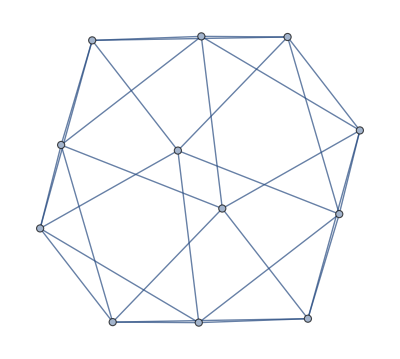

```mathematica
Graph[ReadGrof[6985],GraphLayout->"SpringElectricalEmbedding"]
```

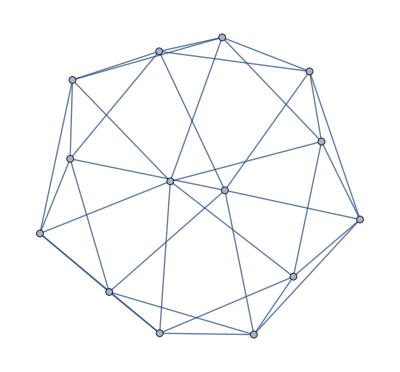

```mathematica
Graph[ReadGrof[279676],GraphLayout->"SpringElectricalEmbedding"]
```

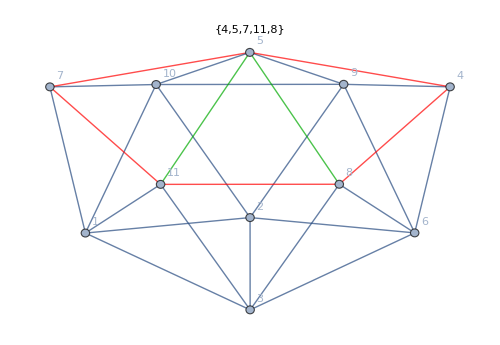
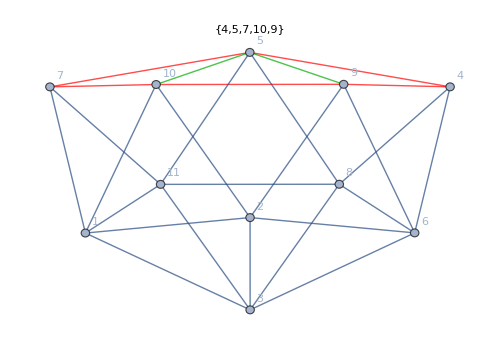
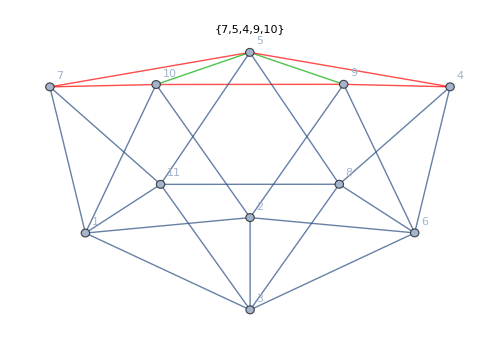
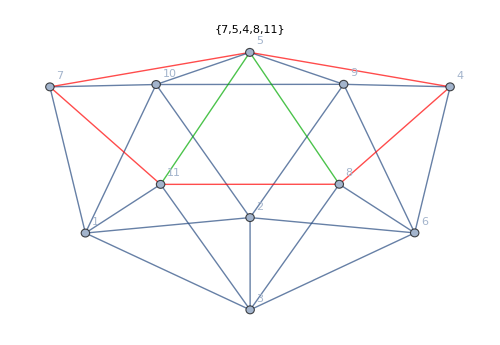

```mathematica
Map[
Graph[ReadGrof[#[[1]]], VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding",EdgeStyle->
Join[
Map[#->Red&,Rule3Cycle[#[[3,2]]]],
Map[#->Darker[Green]&,#[[3,3]]]
], GraphHighlightStyle->"VertexDiamond", ImageSize->500,PlotLabel->#[[3,2]]]&,
Join[Select[deps3,#[[2]]==6985&],Select[deps3Bis,#[[2]]==6985&]]
]
```

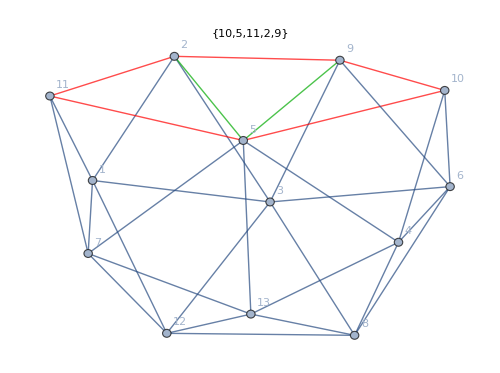
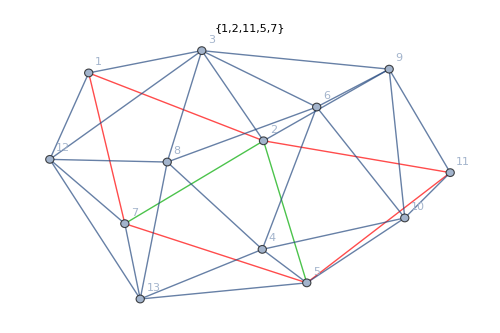
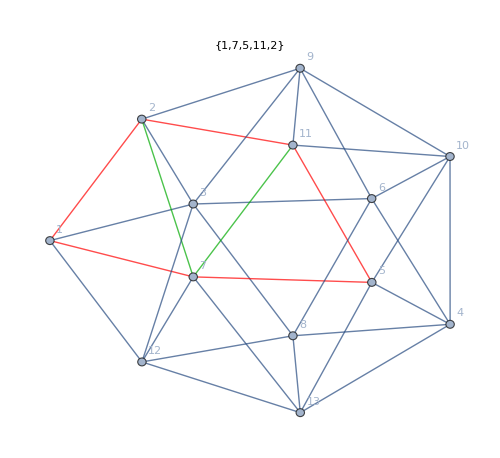
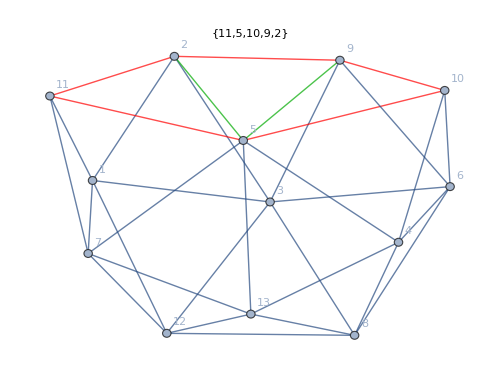
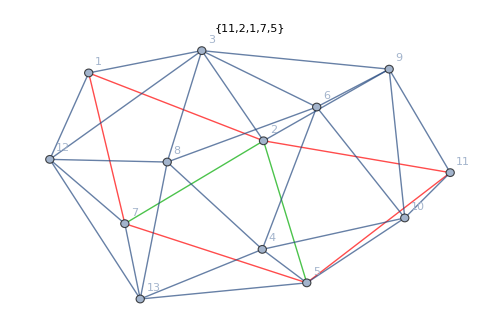
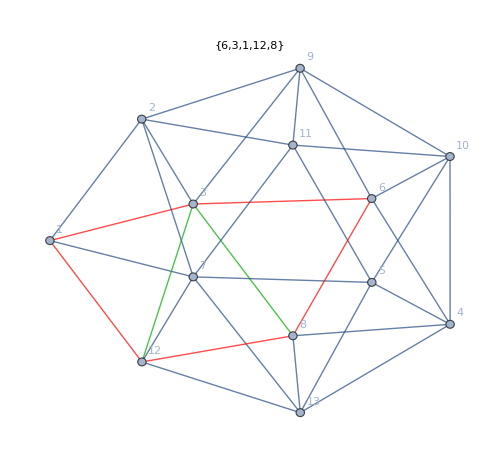
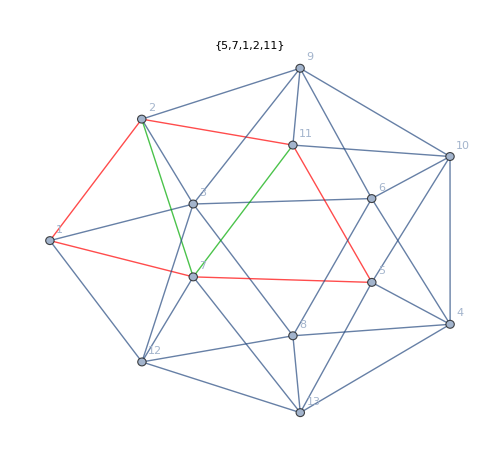
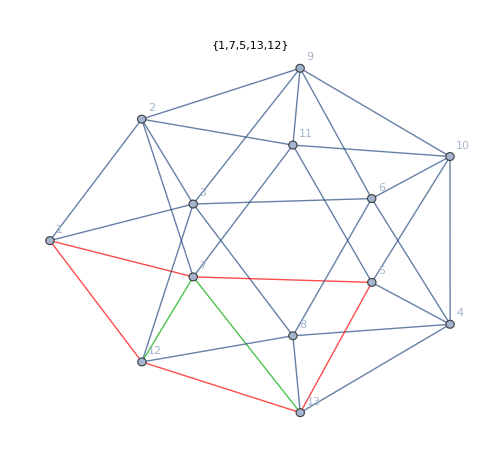

```mathematica
Map[
Graph[ReadGrof[#[[1]]], VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding",EdgeStyle->
Join[
Map[#->Red&,Rule3Cycle[#[[3,2]]]],
Map[#->Darker[Green]&,#[[3,3]]]
], GraphHighlightStyle->"VertexDiamond", ImageSize->500,PlotLabel->#[[3,2]]]&,
Join[Select[deps3,#[[2]]==279676&],Select[deps3Bis,#[[2]]==279676&]]
]
```

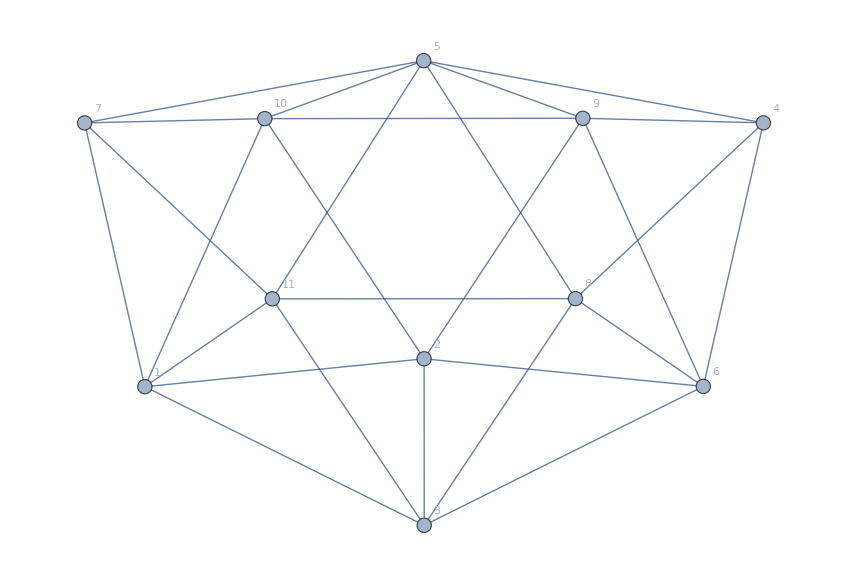

```mathematica
Graph[ReadGrof[897], GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

```mathematica
Graph[ReadGrof[6985], GraphLayout->{ "CircularEmbedding","EdgeLayout"->"HierarchicalEdgeBundling"}, VertexLabels->"Name"]
```

Graph::moptx: Method option "EdgeLayout" in "CircularEmbedding" is not one of {"Offset"}.

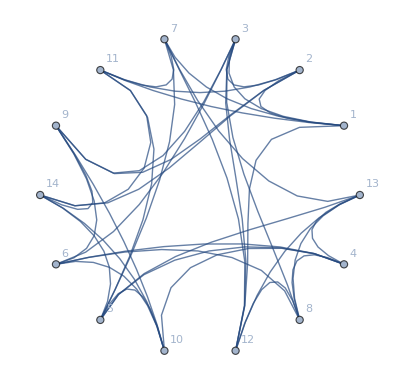

```mathematica
Graph[ReadGrof[279676], GraphLayout->{ "EdgeLayout"->"HierarchicalEdgeBundling"}, VertexLabels->"Name"]
```

```mathematica
Table[IsomorphicGraphQ[ReadGrof[279676],GraphData[name]],{name, GraphData[13]}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
EdgeList[ReadGrof[279676]]
```

{1<->2,1<->3,1<->7,1<->11,1<->12,2<->3,2<->9,2<->11,2<->14,3<->6,3<->8,3<->9,3<->12,4<->5,4<->6,4<->8,4<->10,4<->13,5<->7,5<->10,5<->11,5<->13,5<->14,6<->8,6<->9,6<->10,7<->11,7<->12,7<->13,8<->12,8<->13,9<->10,9<->14,10<->14,11<->14,12<->13}

```mathematica
GraphSignature[279676]
```

6-6-5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
GraphSignature[897]
```

6-5-5-5-5-5-5-5-5-4-4

```mathematica
897
```